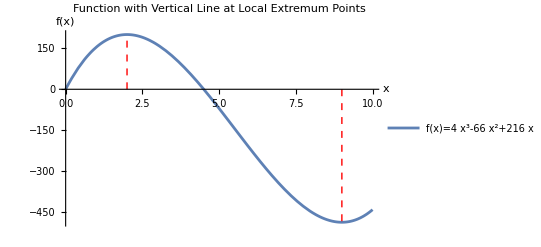

pi

```mathematica
(* Plot the function graph and represent the local extremum with a vertical line *)
(* The stagnation point is obtained according to the first derivative, and the local extremum is obtained *)

(* Step1 Enter funtion *)
f[x_]:=216x-66x^2+4x^3;
fPrime[x_]=D[f[x],x];

(* Step2 Determine the value range *)
criticalPoints=x/. NSolve[fPrime[x]==0&&0<x<10,x];

(* Step3 Determine the plot range *)
Plot[f[x],{x,0,10},
Epilog->{
Red,
Dashed,
Map[Line[{{#,0},{#,f[#]}}]&,criticalPoints] 
},
PlotRange->Full,
PlotLegends->{"f(x)="<>ToString@TraditionalForm@f[x]},
AxesLabel->{"x","f(x)"},
PlotLabel->"Function with Vertical Line at Local Extremum Points"
]
```